### Henry Rachootin

```mathematica
normalize[s_List]:=s/Total[s]
update[p_List,l_List]:=normalize[p*l]
```

### Flea Beetle Problem

Con | Hei | Hep
0.999289 | 0.000710591 | 0.

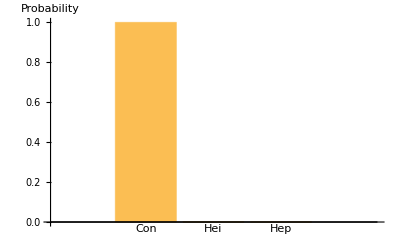

```mathematica
Data={{150,15,Con},{147,13,Con},{144,14,Con},{144,16,Con},{153,13,Con},{140,15,Con},{151,14,Con},{143,14,Con},{144,14,Con},{142,15,Con},{141,13,Con},{150,15,Con},{148,13,Con},{154,15,Con},{147,14,Con},{137,14,Con},{134,15,Con},{157,14,Con},{149,13,Con},{147,13,Con},{148,14,Con},{120,14,Hei},{123,16,Hei},{130,14,Hei},{131,16,Hei},{116,16,Hei},{122,15,Hei},{127,15,Hei},{132,16,Hei},{125,14,Hei},{119,13,Hei},{122,13,Hei},{120,15,Hei},{119,14,Hei},{123,15,Hei},{125,15,Hei},{125,14,Hei},{129,14,Hei},{130,13,Hei},{129,13,Hei},{122,12,Hei},{129,15,Hei},{124,15,Hei},{120,13,Hei},{119,16,Hei},{119,14,Hei},{133,13,Hei},{121,15,Hei},{128,14,Hei},{129,14,Hei},{124,13,Hei},{129,14,Hei},{145,8,Hep},{140,11,Hep},{140,11,Hep},{131,10,Hep},{139,11,Hep},{139,10,Hep},{136,12,Hep},{129,11,Hep},{140,10,Hep},{137,9,Hep},{141,11,Hep},{138,9,Hep},{143,9,Hep},{142,11,Hep},{144,10,Hep},{138,10,Hep},{140,10,Hep},{130,9,Hep},{137,11,Hep},{137,10,Hep},{136,9,Hep},{140,10,Hep}};
ConData=Select[Data,#[[3]]==Con&];
HeiData=Select[Data,#[[3]]==Hei&];
HepData=Select[Data,#[[3]]==Hep&];
names={"Con","Hei","Hep"};
{conW,conA}=SmoothKernelDistribution/@(ConDataᵀ[[1;;2,All]]);
{heiW,heiA}=SmoothKernelDistribution/@(HeiDataᵀ[[1;;2,All]]);
{hepW,hepA}=SmoothKernelDistribution/@(HepDataᵀ[[1;;2,All]]);

prior={1,1,1};
likeW=PDF[#,140]&/@{conW,heiW,hepW};
likeA=PDF[#,15]&/@{conA,heiA,hepA};
post=update[prior,likeW*likeA];
{names,post}//TableForm
BarChart[post,ChartLabels->names,AxesLabel->{,"Probability"}]
```

It' s definitely a con beetle.

### The Alien Blaster Problem

Prior mean | Posterior mean
0.333333 | 0.319328

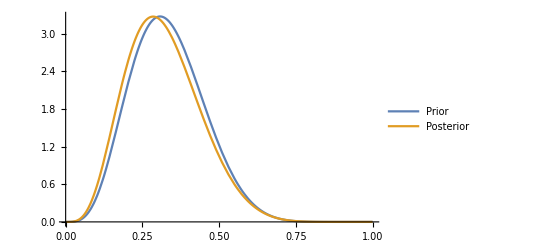

```mathematica
xPrior=BetaDistribution[5,10];
PrMean=Mean[xPrior];
like[x_]:=x^2+(1-x)^2(*Two hits or two misses*)
T=Integrate[PDF[xPrior,x]like[x],{x,0,1}];
xPost[x_]:=PDF[xPrior,x]like[x]/T;
PoMean=Mean[ProbabilityDistribution[xPost[x],{x,0,1}]];
{{"Prior mean","Posterior mean"},{PrMean,PoMean}}//N//TableForm
Plot[{PDF[xPrior,x],xPost[x]},{x,0,1},PlotLegends->{"Prior","Posterior"}]
```

I now think that the alien blaster 9000 is probably a little worse.

### The grizzly bear problem

```mathematica
like[NN_,n_,x_]:=PDF[BinomialDistribution[NN,x],n]
(*NN: number of bears.
n: number of bears sampled.
 x: probability of sampling a bear*)
like[NN_,x_]:=like[NN,23,x]*like[NN-23,19-4,x]*like[23,4,x]
(*saw 23 out of NN, then 19 of the rest, then 4 of the 23*)
likes=Table[N@like[NN,x],{NN,100,500},{x,Array[#&,100,{0,1}]}];
post=likes/Total@Total@likes;
```

```mathematica
ListContourPlot[post,AspectRatio->1,PlotRange->All,DataRange->{{0,1},{0,500}},PlotLegends->Automatic,FrameLabel->{"x","N"},PlotLabel->"Joint PMF"]
```

-Graphics-

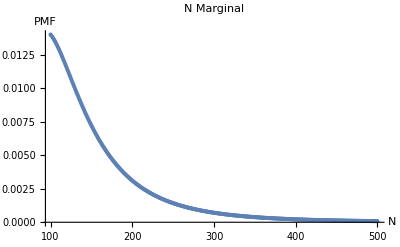

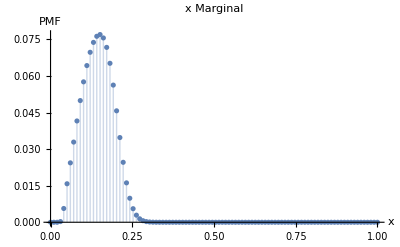

The mean number of bears is:

165.744

```mathematica
NMarginal=normalize[Total/@post];
xMarginal=normalize[Total[post]];
ListPlot[NMarginal,DataRange->{100,500},AxesLabel->{"N","PMF"},PlotLabel->"N Marginal"]
ListPlot[xMarginal,DataRange->{0,1},AxesLabel->{"x","PMF"},PlotLabel->"x Marginal",PlotRange->All,Filling->Axis]
"The mean number of bears is:"
meanN=Total[NMarginal*Table[N,{N,100,500}]]
```

### The World Cup Problem 2

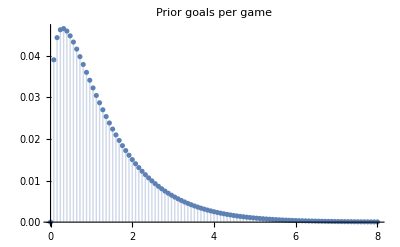

PoissonDistribution::posprm: Parameter 0 at position 1 in PoissonDistribution[0] is expected to be positive.

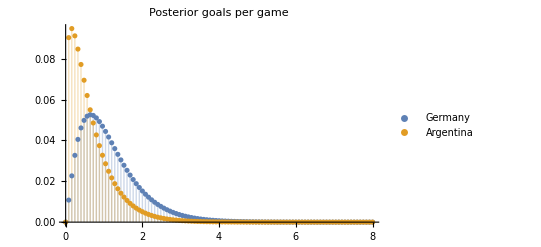

This looks like it gives some evidence that Germany has a better team. Germany's posterior mean λ is

1.15063

While Argentina's is

0.669382

```mathematica
gammaD[x_,a_]:=x^(a-1)Exp[-x]/Gamma[a]
λs=Array[#&,101,{0,8}];
λprior=normalize@Table[gammaD[λ,1.3],{λ,λs}];
ListPlot[{λs,λprior}ᵀ,Filling->Axis,PlotLabel->"Prior goals per game"]
like[n_,λ_]:=PDF[PoissonDistribution[λ],n]
Alike=Table[like[0,λ],{λ,λs}];
Apost=update[λprior,Alike];
Glike=Table[like[1,λ],{λ,λs}];
Gpost=update[λprior,Glike];
ListPlot[{{λs,Gpost}ᵀ,{λs,Apost}ᵀ},Filling->Axis,PlotLabel->"Posterior goals per game",PlotRange->All,PlotLegends->{"Germany","Argentina"}]
"This looks like it gives some evidence that Germany has a better team. Germany's posterior mean λ is"
GMean=Total[Gpost*λs]
"While Argentina's is"
AMean=Total[Apost*λs]
```

```mathematica
jointλP=Table[g*a,{g,Gpost},{a,Apost}];
likeGBetter=Table[If[g>a,1,0],{g,λs},{a,λs}];
"The chance that Germany is better:"
pGBetter=Total[Total[jointλP*likeGBetter]]/Total[Total[jointλP]]
```

The chance that Germany is better:

0.698394

```mathematica
nGoalsP[n_]:=Table[PDF[PoissonDistribution[λ],n],{λ,λs}]
nGoalsP[n_,t_]:=Table[PDF[PoissonDistribution[λ t],n],{λ,λs}]
nGoals=Table[n,{n,0,8}];
gGoalsP=Table[Total[nGoalsP[n]*Gpost],{n,nGoals}];
aGoalsP=Table[Total[nGoalsP[n]*Apost],{n,nGoals}];
GoalsPJoint=Table[a*g,{a,aGoalsP},{g,gGoalsP}];
likeGWins=Table[If[g>a,1,0],{a,nGoals},{g,nGoals}];
likeAWins=Table[If[a>g,1,0],{a,nGoals},{g,nGoals}];
likeOT=Table[If[a==g,1,0],{a,nGoals},{g,nGoals}];

(*probabilities to win or tie before overtime*)
pGWinsNoOt=Total[Total[GoalsPJoint*likeGWins]]/Total[Total[GoalsPJoint]];
pAWinsNoOt=Total[Total[GoalsPJoint*likeAWins]]/Total[Total[GoalsPJoint]];
pOt=Total[Total[GoalsPJoint*likeOT]]/Total[Total[GoalsPJoint]];

(*probabilities to win or tie during overtime*)
gGoalsOTP=Table[Total[nGoalsP[n,1/3]*Gpost],{n,nGoals}];
aGoalsOTP=Table[Total[nGoalsP[n,1/3]*Apost],{n,nGoals}];
GoalsOTPJoint=Table[a*g,{a,aGoalsOTP},{g,gGoalsOTP}];

(*probabilities to win or tie in general*)
pGWinsOt=Total[Total[GoalsOTPJoint*likeGWins]]/Total[Total[GoalsOTPJoint]];
pAWinsOt=Total[Total[GoalsOTPJoint*likeAWins]]/Total[Total[GoalsOTPJoint]];
pOTTie(*heh*)=Total[Total[GoalsOTPJoint*likeOT]]/Total[Total[GoalsOTPJoint]];

pGWins=pGWinsNoOt+pOt*pGWinsOt;
pAWins=pAWinsNoOt+pOt*pAWinsOt;
pDraw=pOt*pOTTie;
"Predictive probabilities for another game:"
{{"Germany wins","Argentina wins","Draw"},{pGWins,pAWins,pDraw}}//TableForm
```

PoissonDistribution::posprm: Parameter 0 at position 1 in PoissonDistribution[0] is expected to be positive.

General::stop: Further output of PoissonDistribution::posprm will be suppressed during this calculation.

PoissonDistribution::posprm: Parameter 0 at position 1 in PoissonDistribution[0] is expected to be positive.

General::stop: Further output of PoissonDistribution::posprm will be suppressed during this calculation.

PoissonDistribution::posprm: Parameter 0 at position 1 in PoissonDistribution[0] is expected to be positive.

General::stop: Further output of PoissonDistribution::posprm will be suppressed during this calculation.

PoissonDistribution::posprm: Parameter 0 at position 1 in PoissonDistribution[0] is expected to be positive.

General::stop: Further output of PoissonDistribution::posprm will be suppressed during this calculation.

Predictive probabilities for another game:

Germany wins | Argentina wins | Draw
0.530564 | 0.270534 | 0.198902

### The game of Ur problem

Before getting any data we have not reason to suspect any particular number of turns has passed, so I’ll use an even prior.

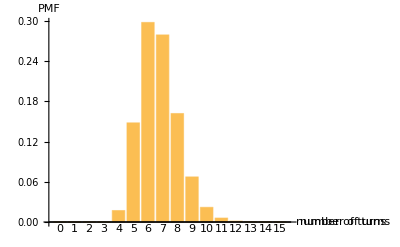

Average number of turns

6.74997

```mathematica
p[k_,n_]:=PDF[BinomialDistribution[4n,0.5],k]
post=normalize[Table[p[13,n],{n,0,15}]];
nTurns=Table[n,{n,0,15}];
BarChart[post,ChartLabels->Table[k,{k,0,15}],AxesLabel->{"number of turns","PMF"}]
"Average number of turns"
Total[nTurns*post]
```